```mathematica
$Assumptions={p>0,ϕj>0,ϕ>0,Temp>0,Element[{y,yj,p},Reals]}
```

{p>0,ϕj>0,ϕ>0,True,(y|yj|p)∈Reals}

```mathematica
expre[y_,p_,ϕ_]:=Cosh[y-yj] p^2/Temp^5 Exp[-p/Temp Cosh[y-yj]](3 Cos[ϕ-ϕj]+Cosh[yj]Cosh[y-yj])
```

```mathematica
Nexpre[y_,p_,ϕ_]:=Abs[Cosh[y-yj] p^2/Temp^5 Exp[-p/Temp Cosh[y-yj]](Cos[ϕ-ϕj]+Cosh[yj]Cosh[y-yj]/3)ΔE/32/Pi]
```

```mathematica
Nexpre[y,p,ϕ]
```

31.0849 ⅇ^(-5. Re[p Cosh[y-yj]]) Abs[p^2 ΔE Cosh[y-yj] (Cos[ϕ-ϕj]+1/3 Cosh[y-yj] Cosh[yj])]

```mathematica
delE:=NIntegrate[p^2 Cosh[y-yj] Nexpre[y,p,ϕ]/.yj->0/.ϕj->0/.ΔE->12,{p,0,Infinity},{y,-Infinity,Infinity},{ϕ,0,2Pi}]
```

```mathematica
delE
```

20.

```mathematica
medN:=NIntegrate[p Nexpre[y,p,ϕ]/.yj->0/.ϕj->0/.ΔE->12,{p,0,Infinity},{y,-Infinity,Infinity},{ϕ,0,2Pi}]
```

```mathematica
medN
```

25.

```mathematica
expre[y,p,ϕ]
```

3125. ⅇ^(-5. p Cosh[y-yj]) p^2 Cosh[y-yj] (3 Cos[ϕ-ϕj]+Cosh[y-yj] Cosh[yj])

```mathematica
exppy[ϕ_]:=NIntegrate[p expre[y,p,ϕ]/.yj->0/.ϕj->0,{p,0,Infinity},{y,-Infinity,Infinity}]
```

```mathematica
exppϕ[y_]:=NIntegrate[p expre[y,p,ϕ]/.yj->0/.ϕj->0,{p,0,Infinity},{ϕ,0,2 Pi}]
```

```mathematica
expyϕ[p_]:=NIntegrate[expre[y,p,ϕ]/.yj->0/.ϕj->0,{y,-Infinity,Infinity},{ϕ,0,2 Pi}]
```

```mathematica
Temp=0.2;
```

```mathematica
Tbp=Table[{p,p expyϕ[p]},{p,0,5,0.05}]//TableForm
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
ArcSinh[3.626860]
```

2.

```mathematica
(Exp[2.]-Exp[-2])/2
```

3.62686

```mathematica
5.43^2+1.4^2
```

31.4449

```mathematica
Sqrt[%]
```

5.60758

```mathematica
$Assumptions={xss>0}
```

{xss>0}

```mathematica
{xss>0}
```

```mathematica
xs=0.2*100^(1/3)/2/0.2^(4/3)/0.15
```

26.4567

```mathematica
Integrate[x^2/Sqrt[xss^2-x^2],{x,0,20}]
```

ConditionalExpression[-10 √(-400+xss^2)+1/2 xss^2 ArcSin[20/xss],xss>20]

```mathematica
-10 √(-400+xss^2)+1/2 xss^2 ArcSin[20./xss]/.xss->26.4567
```

```mathematica
126.7765042510654*4/Pi/xs^2*100.
```

```mathematica
(23.061-23.082)/(23.061)
```

-0.000910628

```mathematica
Eout:=Ein*(1-)
```

```mathematica
Tby=Table[{y, exppϕ[y]},{y,-10,10,0.1}]//TableForm
```

-10. | 1.55407×10^-6
-9.9 | 1.89815×10^-6
-9.8 | 2.3184×10^-6
-9.7 | 2.83171×10^-6
-9.6 | 3.45865×10^-6
-9.5 | 4.22441×10^-6
-9.4 | 5.1597×10^-6
-9.3 | 6.30208×10^-6
-9.2 | 7.69737×10^-6
-9.1 | 9.40159×10^-6
-9. | 0.0000114831
-8.9 | 0.0000140255
-8.8 | 0.0000171308
-8.7 | 0.0000209236
-8.6 | 0.0000255562
-8.5 | 0.0000312144
-8.4 | 0.0000381253
-8.3 | 0.0000465664
-8.2 | 0.0000568763
-8.1 | 0.0000694689
-8. | 0.0000848495
-7.9 | 0.000103635
-7.8 | 0.000126581
-7.7 | 0.000154606
-7.6 | 0.000188836
-7.5 | 0.000230645
-7.4 | 0.00028171
-7.3 | 0.000344081
-7.2 | 0.000420262
-7.1 | 0.000513309
-7. | 0.000626957
-6.9 | 0.000765766
-6.8 | 0.000935309
-6.7 | 0.00114239
-6.6 | 0.00139532
-6.5 | 0.00170424
-6.4 | 0.00208156
-6.3 | 0.00254242
-6.2 | 0.00310532
-6.1 | 0.00379284
-6. | 0.00463257
-5.9 | 0.00565822
-5.8 | 0.00691094
-5.7 | 0.00844101
-5.6 | 0.0103098
-5.5 | 0.0125924
-5.4 | 0.0153802
-5.3 | 0.0187853
-5.2 | 0.0229442
-5.1 | 0.0280237
-5. | 0.0342276
-4.9 | 0.0418049
-4.8 | 0.0510593
-4.7 | 0.0623622
-4.6 | 0.0761665
-4.5 | 0.0930258
-4.4 | 0.113616
-4.3 | 0.138761
-4.2 | 0.16947
-4.1 | 0.20697
-4. | 0.252763
-3.9 | 0.30868
-3.8 | 0.376954
-3.7 | 0.460311
-3.6 | 0.562073
-3.5 | 0.686291
-3.4 | 0.837899
-3.3 | 1.02291
-3.2 | 1.24863
-3.1 | 1.52396
-3. | 1.8597
-2.9 | 2.26896
-2.8 | 2.76762
-2.7 | 3.37487
-2.6 | 4.11388
-2.5 | 5.01252
-2.4 | 6.10419
-2.3 | 7.42881
-2.2 | 9.03371
-2.1 | 10.9748
-2. | 13.3174
-1.9 | 16.1371
-1.8 | 19.5203
-1.7 | 23.5638
-1.6 | 28.3737
-1.5 | 34.0624
-1.4 | 40.7438
-1.3 | 48.525
-1.2 | 57.4949
-1.1 | 67.7079
-1. | 79.1633
-0.9 | 91.7818
-0.8 | 105.379
-0.7 | 119.646
-0.6 | 134.129
-0.5 | 148.242
-0.4 | 161.284
-0.3 | 172.499
-0.2 | 181.152
-0.1 | 186.623
0. | 188.496
0.1 | 186.623
0.2 | 181.152
0.3 | 172.499
0.4 | 161.284
0.5 | 148.242
0.6 | 134.129
0.7 | 119.646
0.8 | 105.379
0.9 | 91.7818
1. | 79.1633
1.1 | 67.7079
1.2 | 57.4949
1.3 | 48.525
1.4 | 40.7438
1.5 | 34.0624
1.6 | 28.3737
1.7 | 23.5638
1.8 | 19.5203
1.9 | 16.1371
2. | 13.3174
2.1 | 10.9748
2.2 | 9.03371
2.3 | 7.42881
2.4 | 6.10419
2.5 | 5.01252
2.6 | 4.11388
2.7 | 3.37487
2.8 | 2.76762
2.9 | 2.26896
3. | 1.8597
3.1 | 1.52396
3.2 | 1.24863
3.3 | 1.02291
3.4 | 0.837899
3.5 | 0.686291
3.6 | 0.562073
3.7 | 0.460311
3.8 | 0.376954
3.9 | 0.30868
4. | 0.252763
4.1 | 0.20697
4.2 | 0.16947
4.3 | 0.138761
4.4 | 0.113616
4.5 | 0.0930258
4.6 | 0.0761665
4.7 | 0.0623622
4.8 | 0.0510593
4.9 | 0.0418049
5. | 0.0342276
5.1 | 0.0280237
5.2 | 0.0229442
5.3 | 0.0187853
5.4 | 0.0153802
5.5 | 0.0125924
5.6 | 0.0103098
5.7 | 0.00844101
5.8 | 0.00691094
5.9 | 0.00565822
6. | 0.00463257
6.1 | 0.00379284
6.2 | 0.00310532
6.3 | 0.00254242
6.4 | 0.00208156
6.5 | 0.00170424
6.6 | 0.00139532
6.7 | 0.00114239
6.8 | 0.000935309
6.9 | 0.000765766
7. | 0.000626957
7.1 | 0.000513309
7.2 | 0.000420262
7.3 | 0.000344081
7.4 | 0.00028171
7.5 | 0.000230645
7.6 | 0.000188836
7.7 | 0.000154606
7.8 | 0.000126581
7.9 | 0.000103635
8. | 0.0000848495
8.1 | 0.0000694689
8.2 | 0.0000568763
8.3 | 0.0000465664
8.4 | 0.0000381253
8.5 | 0.0000312144
8.6 | 0.0000255562
8.7 | 0.0000209236
8.8 | 0.0000171308
8.9 | 0.0000140255
9. | 0.0000114831
9.1 | 9.40159×10^-6
9.2 | 7.69737×10^-6
9.3 | 6.30208×10^-6
9.4 | 5.1597×10^-6
9.5 | 4.22441×10^-6
9.6 | 3.45865×10^-6
9.7 | 2.83171×10^-6
9.8 | 2.3184×10^-6
9.9 | 1.89815×10^-6
10. | 1.55407×10^-6

```mathematica
Tbphi=Table[{ϕ, exppy[ϕ]},{ϕ,0,2 Pi,0.01}]//TableForm
```

0. | 201.372
0.01 | 201.365
0.02 | 201.343
0.03 | 201.308
0.04 | 201.258
0.05 | 201.195
0.06 | 201.117
0.07 | 201.025
0.08 | 200.919
0.09 | 200.799
0.1 | 200.665
0.11 | 200.517
0.12 | 200.355
0.13 | 200.179
0.14 | 199.988
0.15 | 199.784
0.16 | 199.566
0.17 | 199.334
0.18 | 199.088
0.19 | 198.827
0.2 | 198.554
0.21 | 198.266
0.22 | 197.964
0.23 | 197.649
0.24 | 197.32
0.25 | 196.977
0.26 | 196.62
0.27 | 196.25
0.28 | 195.866
0.29 | 195.468
0.3 | 195.057
0.31 | 194.633
0.32 | 194.195
0.33 | 193.743
0.34 | 193.279
0.35 | 192.801
0.36 | 192.309
0.37 | 191.805
0.38 | 191.287
0.39 | 190.756
0.4 | 190.212
0.41 | 189.655
0.42 | 189.085
0.43 | 188.502
0.44 | 187.906
0.45 | 187.298
0.46 | 186.676
0.47 | 186.042
0.48 | 185.396
0.49 | 184.737
0.5 | 184.065
0.51 | 183.381
0.52 | 182.685
0.53 | 181.976
0.54 | 181.256
0.55 | 180.523
0.56 | 179.778
0.57 | 179.021
0.58 | 178.252
0.59 | 177.471
0.6 | 176.679
0.61 | 175.875
0.62 | 175.059
0.63 | 174.232
0.64 | 173.394
0.65 | 172.544
0.66 | 171.682
0.67 | 170.81
0.68 | 169.927
0.69 | 169.032
0.7 | 168.127
0.71 | 167.211
0.72 | 166.284
0.73 | 165.346
0.74 | 164.398
0.75 | 163.44
0.76 | 162.471
0.77 | 161.492
0.78 | 160.503
0.79 | 159.504
0.8 | 158.494
0.81 | 157.475
0.82 | 156.447
0.83 | 155.408
0.84 | 154.36
0.85 | 153.303
0.86 | 152.236
0.87 | 151.16
0.88 | 150.075
0.89 | 148.981
0.9 | 147.878
0.91 | 146.766
0.92 | 145.646
0.93 | 144.517
0.94 | 143.379
0.95 | 142.233
0.96 | 141.079
0.97 | 139.917
0.98 | 138.747
0.99 | 137.569
1. | 136.383
1.01 | 135.19
1.02 | 133.989
1.03 | 132.781
1.04 | 131.565
1.05 | 130.342
1.06 | 129.113
1.07 | 127.876
1.08 | 126.632
1.09 | 125.382
1.1 | 124.126
1.11 | 122.862
1.12 | 121.593
1.13 | 120.318
1.14 | 119.036
1.15 | 117.748
1.16 | 116.455
1.17 | 115.156
1.18 | 113.852
1.19 | 112.542
1.2 | 111.227
1.21 | 109.907
1.22 | 108.582
1.23 | 107.252
1.24 | 105.917
1.25 | 104.578
1.26 | 103.234
1.27 | 101.886
1.28 | 100.533
1.29 | 99.1769
1.3 | 97.8167
1.31 | 96.4526
1.32 | 95.0849
1.33 | 93.7137
1.34 | 92.3391
1.35 | 90.9612
1.36 | 89.5803
1.37 | 88.1964
1.38 | 86.8097
1.39 | 85.4204
1.4 | 84.0284
1.41 | 82.6341
1.42 | 81.2375
1.43 | 79.8388
1.44 | 78.4381
1.45 | 77.0356
1.46 | 75.6313
1.47 | 74.2255
1.48 | 72.8183
1.49 | 71.4098
1.5 | 70.0001
1.51 | 68.5895
1.52 | 67.178
1.53 | 65.7657
1.54 | 64.3529
1.55 | 62.9397
1.56 | 61.5262
1.57 | 60.1125
1.58 | 58.6988
1.59 | 57.2852
1.6 | 55.8719
1.61 | 54.459
1.62 | 53.0467
1.63 | 51.6351
1.64 | 50.2243
1.65 | 48.8144
1.66 | 47.4057
1.67 | 45.9983
1.68 | 44.5923
1.69 | 43.1878
1.7 | 41.7849
1.71 | 40.3839
1.72 | 38.9849
1.73 | 37.588
1.74 | 36.1933
1.75 | 34.801
1.76 | 33.4112
1.77 | 32.024
1.78 | 30.6397
1.79 | 29.2583
1.8 | 27.88
1.81 | 26.5048
1.82 | 25.1331
1.83 | 23.7648
1.84 | 22.4001
1.85 | 21.0392
1.86 | 19.6822
1.87 | 18.3293
1.88 | 16.9805
1.89 | 15.636
1.9 | 14.2959
1.91 | 12.9604
1.92 | 11.6296
1.93 | 10.3037
1.94 | 8.9827
1.95 | 7.66682
1.96 | 6.35617
1.97 | 5.05089
1.98 | 3.7511
1.99 | 2.45694
2. | 1.16853
2.01 | -0.113999
2.02 | -1.39051
2.03 | -2.66089
2.04 | -3.925
2.05 | -5.18272
2.06 | -6.43391
2.07 | -7.67847
2.08 | -8.91626
2.09 | -10.1472
2.1 | -11.371
2.11 | -12.5878
2.12 | -13.7973
2.13 | -14.9994
2.14 | -16.194
2.15 | -17.381
2.16 | -18.5602
2.17 | -19.7316
2.18 | -20.895
2.19 | -22.0504
2.2 | -23.1975
2.21 | -24.3363
2.22 | -25.4667
2.23 | -26.5885
2.24 | -27.7017
2.25 | -28.8061
2.26 | -29.9016
2.27 | -30.9881
2.28 | -32.0655
2.29 | -33.1337
2.3 | -34.1927
2.31 | -35.2421
2.32 | -36.2821
2.33 | -37.3124
2.34 | -38.333
2.35 | -39.3438
2.36 | -40.3447
2.37 | -41.3355
2.38 | -42.3161
2.39 | -43.2866
2.4 | -44.2467
2.41 | -45.1964
2.42 | -46.1355
2.43 | -47.0641
2.44 | -47.9819
2.45 | -48.889
2.46 | -49.7851
2.47 | -50.6703
2.48 | -51.5444
2.49 | -52.4074
2.5 | -53.2591
2.51 | -54.0995
2.52 | -54.9285
2.53 | -55.746
2.54 | -56.5519
2.55 | -57.3462
2.56 | -58.1287
2.57 | -58.8994
2.58 | -59.6582
2.59 | -60.4051
2.6 | -61.1399
2.61 | -61.8626
2.62 | -62.5731
2.63 | -63.2714
2.64 | -63.9573
2.65 | -64.6308
2.66 | -65.2919
2.67 | -65.9405
2.68 | -66.5764
2.69 | -67.1997
2.7 | -67.8103
2.71 | -68.4081
2.72 | -68.993
2.73 | -69.5651
2.74 | -70.1242
2.75 | -70.6703
2.76 | -71.2033
2.77 | -71.7232
2.78 | -72.2299
2.79 | -72.7234
2.8 | -73.2036
2.81 | -73.6706
2.82 | -74.1241
2.83 | -74.5642
2.84 | -74.9909
2.85 | -75.4041
2.86 | -75.8037
2.87 | -76.1898
2.88 | -76.5622
2.89 | -76.921
2.9 | -77.2661
2.91 | -77.5974
2.92 | -77.915
2.93 | -78.2189
2.94 | -78.5088
2.95 | -78.785
2.96 | -79.0472
2.97 | -79.2956
2.98 | -79.53
2.99 | -79.7505
3. | -79.957
3.01 | -80.1495
3.02 | -80.328
3.03 | -80.4924
3.04 | -80.6428
3.05 | -80.7792
3.06 | -80.9015
3.07 | -81.0096
3.08 | -81.1037
3.09 | -81.1837
3.1 | -81.2495
3.11 | -81.3012
3.12 | -81.3388
3.13 | -81.3623
3.14 | -81.3716
3.15 | -81.3668
3.16 | -81.3478
3.17 | -81.3147
3.18 | -81.2675
3.19 | -81.2062
3.2 | -81.1307
3.21 | -81.0411
3.22 | -80.9374
3.23 | -80.8197
3.24 | -80.6878
3.25 | -80.5419
3.26 | -80.3819
3.27 | -80.2079
3.28 | -80.0198
3.29 | -79.8178
3.3 | -79.6018
3.31 | -79.3718
3.32 | -79.1279
3.33 | -78.87
3.34 | -78.5983
3.35 | -78.3127
3.36 | -78.0133
3.37 | -77.7001
3.38 | -77.3731
3.39 | -77.0324
3.4 | -76.678
3.41 | -76.3099
3.42 | -75.9282
3.43 | -75.5329
3.44 | -75.124
3.45 | -74.7016
3.46 | -74.2658
3.47 | -73.8165
3.48 | -73.3538
3.49 | -72.8778
3.5 | -72.3885
3.51 | -71.886
3.52 | -71.3703
3.53 | -70.8415
3.54 | -70.2995
3.55 | -69.7446
3.56 | -69.1767
3.57 | -68.5958
3.58 | -68.0021
3.59 | -67.3956
3.6 | -66.7763
3.61 | -66.1444
3.62 | -65.4999
3.63 | -64.8428
3.64 | -64.1732
3.65 | -63.4912
3.66 | -62.7969
3.67 | -62.0902
3.68 | -61.3714
3.69 | -60.6404
3.7 | -59.8974
3.71 | -59.1424
3.72 | -58.3755
3.73 | -57.5967
3.74 | -56.8062
3.75 | -56.0039
3.76 | -55.1901
3.77 | -54.3648
3.78 | -53.528
3.79 | -52.6799
3.8 | -51.8205
3.81 | -50.95
3.82 | -50.0683
3.83 | -49.1756
3.84 | -48.272
3.85 | -47.3576
3.86 | -46.4325
3.87 | -45.4967
3.88 | -44.5503
3.89 | -43.5935
3.9 | -42.6264
3.91 | -41.6489
3.92 | -40.6614
3.93 | -39.6637
3.94 | -38.6561
3.95 | -37.6386
3.96 | -36.6114
3.97 | -35.5744
3.98 | -34.528
3.99 | -33.4721
4. | -32.4068
4.01 | -31.3323
4.02 | -30.2486
4.03 | -29.156
4.04 | -28.0544
4.05 | -26.944
4.06 | -25.8249
4.07 | -24.6973
4.08 | -23.5611
4.09 | -22.4167
4.1 | -21.2639
4.11 | -20.1031
4.12 | -18.9342
4.13 | -17.7574
4.14 | -16.5729
4.15 | -15.3807
4.16 | -14.181
4.17 | -12.9738
4.18 | -11.7594
4.19 | -10.5378
4.2 | -9.30909
4.21 | -8.07348
4.22 | -6.83107
4.23 | -5.58197
4.24 | -4.32632
4.25 | -3.06423
4.26 | -1.79584
4.27 | -0.521266
4.28 | 0.759359
4.29 | 2.0459
4.3 | 3.33825
4.31 | 4.63626
4.32 | 5.93981
4.33 | 7.24876
4.34 | 8.56299
4.35 | 9.88236
4.36 | 11.2067
4.37 | 12.536
4.38 | 13.87
4.39 | 15.2086
4.4 | 16.5517
4.41 | 17.8992
4.42 | 19.2508
4.43 | 20.6066
4.44 | 21.9662
4.45 | 23.3297
4.46 | 24.6969
4.47 | 26.0675
4.48 | 27.4416
4.49 | 28.8189
4.5 | 30.1993
4.51 | 31.5828
4.52 | 32.969
4.53 | 34.358
4.54 | 35.7495
4.55 | 37.1435
4.56 | 38.5397
4.57 | 39.9381
4.58 | 41.3385
4.59 | 42.7407
4.6 | 44.1447
4.61 | 45.5503
4.62 | 46.9573
4.63 | 48.3656
4.64 | 49.7751
4.65 | 51.1856
4.66 | 52.597
4.67 | 54.0091
4.68 | 55.4218
4.69 | 56.835
4.7 | 58.2485
4.71 | 59.6622
4.72 | 61.0759
4.73 | 62.4895
4.74 | 63.9028
4.75 | 65.3158
4.76 | 66.7282
4.77 | 68.14
4.78 | 69.5509
4.79 | 70.9609
4.8 | 72.3698
4.81 | 73.7774
4.82 | 75.1837
4.83 | 76.5885
4.84 | 77.9916
4.85 | 79.3929
4.86 | 80.7922
4.87 | 82.1895
4.88 | 83.5846
4.89 | 84.9773
4.9 | 86.3675
4.91 | 87.755
4.92 | 89.1398
4.93 | 90.5217
4.94 | 91.9005
4.95 | 93.2762
4.96 | 94.6485
4.97 | 96.0173
4.98 | 97.3826
4.99 | 98.7441
5. | 100.102
5.01 | 101.455
5.02 | 102.805
5.03 | 104.15
5.04 | 105.491
5.05 | 106.827
5.06 | 108.159
5.07 | 109.485
5.08 | 110.807
5.09 | 112.124
5.1 | 113.435
5.11 | 114.741
5.12 | 116.042
5.13 | 117.337
5.14 | 118.626
5.15 | 119.91
5.16 | 121.187
5.17 | 122.459
5.18 | 123.724
5.19 | 124.983
5.2 | 126.235
5.21 | 127.481
5.22 | 128.719
5.23 | 129.951
5.24 | 131.176
5.25 | 132.394
5.26 | 133.605
5.27 | 134.808
5.28 | 136.004
5.29 | 137.192
5.3 | 138.373
5.31 | 139.545
5.32 | 140.71
5.33 | 141.867
5.34 | 143.015
5.35 | 144.155
5.36 | 145.287
5.37 | 146.41
5.38 | 147.525
5.39 | 148.631
5.4 | 149.727
5.41 | 150.815
5.42 | 151.894
5.43 | 152.964
5.44 | 154.024
5.45 | 155.075
5.46 | 156.117
5.47 | 157.149
5.48 | 158.171
5.49 | 159.183
5.5 | 160.186
5.51 | 161.178
5.52 | 162.16
5.53 | 163.133
5.54 | 164.094
5.55 | 165.046
5.56 | 165.986
5.57 | 166.917
5.58 | 167.836
5.59 | 168.745
5.6 | 169.643
5.61 | 170.53
5.62 | 171.406
5.63 | 172.271
5.64 | 173.124
5.65 | 173.966
5.66 | 174.797
5.67 | 175.616
5.68 | 176.424
5.69 | 177.22
5.7 | 178.005
5.71 | 178.777
5.72 | 179.538
5.73 | 180.287
5.74 | 181.023
5.75 | 181.748
5.76 | 182.461
5.77 | 183.161
5.78 | 183.849
5.79 | 184.524
5.8 | 185.187
5.81 | 185.838
5.82 | 186.476
5.83 | 187.101
5.84 | 187.714
5.85 | 188.314
5.86 | 188.901
5.87 | 189.475
5.88 | 190.036
5.89 | 190.584
5.9 | 191.119
5.91 | 191.641
5.92 | 192.15
5.93 | 192.646
5.94 | 193.128
5.95 | 193.597
5.96 | 194.053
5.97 | 194.495
5.98 | 194.924
5.99 | 195.339
6. | 195.741
6.01 | 196.129
6.02 | 196.504
6.03 | 196.865
6.04 | 197.212
6.05 | 197.545
6.06 | 197.865
6.07 | 198.171
6.08 | 198.463
6.09 | 198.742
6.1 | 199.006
6.11 | 199.257
6.12 | 199.493
6.13 | 199.716
6.14 | 199.925
6.15 | 200.12
6.16 | 200.3
6.17 | 200.467
6.18 | 200.62
6.19 | 200.758
6.2 | 200.883
6.21 | 200.993
6.22 | 201.089
6.23 | 201.172
6.24 | 201.24
6.25 | 201.294
6.26 | 201.334
6.27 | 201.359
6.28 | 201.371

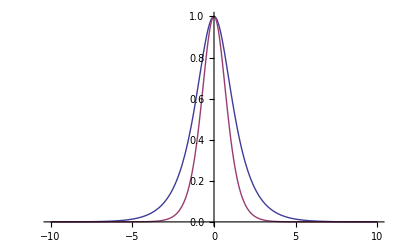

```mathematica
Plot[{1/Cosh[x],1/Cosh[x]^2},{x,-10,10},PlotRange->Full]
```

```mathematica
(-9.75-0.25)/0.5
```

-20.

```mathematica
160.478/118017
```

0.00135979

```mathematica
141-48
```

93

```mathematica
Integrate[1/Cosh[y-yj]^2,{y,-Infinity,Infinity}]
```

2

```mathematica
32*8.4
```

268.8

```mathematica
36.*Pi
```

113.097

```mathematica
141.372/Pi
```

45.0001

```mathematica
Integrate[x^3 Exp[-a x],{x,0,Infinity}]
```

ConditionalExpression[6/a^4,Re[a]>0]

```mathematica
Integrate[1/Cosh[y-yj]^2,{y,-Infinity,Infinity}]
```

ConditionalExpression[2,(Re[ⅇ^-yj]≠0||Im[ⅇ^-yj]<-1||Im[ⅇ^-yj]>1)&&(Re[ⅇ^yj]≠0||Im[ⅇ^yj]<-1||Im[ⅇ^yj]>1)]

```mathematica
96/24
```

4

```mathematica
30/0.8
```

37.5

```mathematica
$Assumptions={Element[{a,x},Reals]}
```

{(a|x)∈Reals}

```mathematica
Integrate[Abs[Cos[x-a]],{x,0,2Pi}]
```

4 Abs[Cos[a]] Tan[a]